```mathematica
DSolve[y''''[x]+y'''[x]+y''[x]+y'[x]==0,y[x],x]
```

{{y[x]→-ⅇ^-x C[3]+C[4]-C[2] Cos[x]+C[1] Sin[x]}}

```mathematica
{{eq}}=DSolve[y'[x]==y[x]^2+x,y[x],x]
```

{{y[x]→(-BesselJ[-1/3,(2 x^(3/2))/3] C[1]+x^(3/2) (-2 BesselJ[-2/3,(2 x^(3/2))/3]-BesselJ[-4/3,(2 x^(3/2))/3] C[1]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(2 x (BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1]))}}

```mathematica
eq2=eq[[2]]/.{C[1]->1}
```

(-BesselJ[-1/3,(2 x^(3/2))/3]+x^(3/2) (-BesselJ[-4/3,(2 x^(3/2))/3]-2 BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3]))/(2 x (BesselJ[-1/3,(2 x^(3/2))/3]+BesselJ[1/3,(2 x^(3/2))/3]))

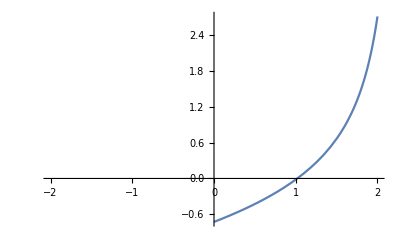

```mathematica
a=2;
Plot[eq2,{x,-a,a}]
```